```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
SetDirectory[basepath<>"/output"];
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
Needs["LatticeAnalysis`"];
 <<"LatticeAnalysis`"
(* do not keep track of intermediate results *)
$HistoryLength=0;
Needs["FourierSeries`"]
lata=0.11403
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

0.11403

#### Open Database

```mathematica
AmpDB = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_bL_bT_bevenodd.bidatex"]
AmpDBPbbsq = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_Pb32by2Pi_bsq_bevenodd.bidatex"]
```

< -MemDB- {A,bL,bNum,bT,data,EN,etav,MN,PL,zta}>

< -MemDB- {A,bNum,bsquare,data,EN,etav,MN,Pb32by2Pi,PL,zta}>

```mathematica
modelfitJackkife[model_, fitParams_, x_, y_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,y,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifefor4D[model_,fitParams_,x_,y_,z_]:=Module[{numFs,modelvaluej,modelvalue,jackknifeResults, numParams},numFs=Length[fitParams[[1]]];
numParams=Length[fitParams];
modelvaluej[j_]:=Module[{datafitParams},datafitParams=Table[fitParams[[k,j]],{k,numParams}];
model[x,y,z,datafitParams]];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@modelvalue;
Return[jackknifeResults];
];
meanfromJK[JKvalue_]:=Module[{meanvalue},
meanvalue = MakeErrBars[{{1,JKvalue}}][[1]][[1]][[2]];
Return[meanvalue];
];
errorfromJK[JKvalue_]:=Module[{errorvalue},
errorvalue = MakeErrBars[{{1,JKvalue}}][[1]][[2]][[1]][[2]];
Return[errorvalue];
];
chisqOEsigmasq[O_, E_]:=Module[{OEsigmasq, Omean,Emean, Esigmasq, Osigmasq, sigmasqTotal},
Omean=meanfromJK[O];
Emean=meanfromJK[E];
Esigmasq = (MakeErrBars[{{1,E}}][[1]][[2]][[1]][[2]])^2;
Osigmasq = (MakeErrBars[{{1,O}}][[1]][[2]][[1]][[2]])^2;
sigmasqTotal = Esigmasq+Osigmasq;
OEsigmasq = If[sigmasqTotal==0,0,((Omean-Emean)^2)/sigmasqTotal];
OEsigmasq
];

JackknifeFit3D[xyJKf_,model_,para_,vari_, modelFnName_]:=Module[
{numFs,fitParamsForFj,fitParamsList,paramLists,jackknifeResults,DoF, chisquare, observed, expected, chisquareperDoF},
numFs=Length[xyJKf[[1,3]]];
(*Function to extract j-th f values and fit them*)
fitParamsForFj[j_]:=Module[{data,fit},
data={#[[1]],#[[2]],#[[3,j]]}&/@xyJKf;(*Extract f_j values*)
fit=NonlinearModelFit[data,model,para,vari];
fit["BestFitParameters"] (*Extract fitted parameters*)
];
(*Compute fit parameters for each f_j*)
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
DoF=Length[xyJKf];
chisquare=0;
Do[
observed = modelfitJackkife[modelFnName, jackknifeResults, xyJKf[[i]][[1]], xyJKf[[i]][[2]]];
expected= xyJKf[[i]][[3]];
chisquare = chisquare + chisqOEsigmasq[observed, expected];
,{i,DoF}];
chisquareperDoF=chisquare/(DoF-3);
{FitParameters->jackknifeResults, chisquareDoF->chisquareperDoF}];

JackknifeFit4D[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,n, k,chisquare,observed,expected,chisquareperDoF,AICvalue, AICcvalue},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[j_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,j]]}&/@nxyJKf;
fit=NonlinearModelFit[data,model,If[init===Automatic,para,init],vari, Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
n=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,n}]];
k =Length[para];
chisquareperDoF=chisquare/(n-k);
AICvalue = (2*k)+chisquare;
AICcvalue =AICvalue +((2*k*(k+1))/(n-k-1));
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF, AIC->AICvalue,AICc->AICcvalue}];

JackknifeFit4DGaussianCons[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,nn, kk,chisquare,observed,expected,chisquareperDoF,AICvalue,AICcvalue},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[i_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,i]]}&/@nxyJKf;
fit=NonlinearModelFit[data,{model, c>d},If[init===Automatic,para,init],vari,Weights->WeightList];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[jj],{jj,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
nn=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,nn}]];
kk =Length[para];
chisquareperDoF=chisquare/(nn-kk);
AICvalue = (2*kk)+chisquare;
AICcvalue =AICvalue +((2*kk*(kk+1))/(nn-kk-1));
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF, AIC->AICvalue,AICc->AICcvalue}];

modelfitJackkifband[model_, fitParams_,fixedVare_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x, fixedVare,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];


modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifex3para[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]],fitParams[[4]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];

modelJackk[model_, fitParam_, multipliar_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParam];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=fitParam[[j]];
model[datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults*multipliar
];
PowerJackk[a_,b_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[b];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=(a)^b[[j]];
datafitParams
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
ExpJackk[b_,eta_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[b];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=Exp[b[[j]]*eta];
datafitParams
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
```

```mathematica
PrintxA2B[ParaFitReA2B_, P1_, b2_]:=Module[{LenPara,fourieReA2Bxforplot, fourierREA2Bforx, II, bsqJK, aReA2B, dReA2B, cReA2B, jReA2B, fourierReA2B, PlotfourieReA2Bx},
LenPara = Length[ParaFitReA2B];
II = ParaFitReA2B[[1]] /ParaFitReA2B[[1]] ;
aReA2B = ParaFitReA2B[[1]] ;
dReA2B=II+ParaFitReA2B[[3]]*b2;
cReA2B=(ParaFitReA2B[[2]])/(P1^2);
jReA2B = ParaFitReA2B[[LenPara ]];

fourierReA2B[x_, {a_,d_,c_,j_}] :=(2^(1-j) a (c/d)^(-(1/4)-j/2) d^-j Abs[x]^(-(1/2)+j) BesselK[1/2-j,Abs[x]/Sqrt[c/d]])/Gamma[j];

fourieReA2Bxforplot={};
Do[
fourierREA2Bforx=modelfitJackkifex[fourierReA2B,{aReA2B,dReA2B,cReA2B,jReA2B}, x];
AppendTo[fourieReA2Bxforplot,{x,fourierREA2Bforx}];
,{x,0,1, 0.005}];
PlotfourieReA2Bx= ErrorListPlot[MakeErrBars[fourieReA2Bxforplot],FrameLabel->{ , "FT[ReA2B]"}, Frame->True , PlotRange->{Full,{0,3}}];
Return[PlotfourieReA2Bx];
];


FitetarangeListReA2B[bminForFit_,momL_,etamin_,etamax_]:=Module[{fitJKA2B,dataforfitA2B,results={},ParaFitReA2B},
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];

modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,j_}]:=(a*Exp[-f*x1])/(1+(d+c)*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,nparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.4},{nparam,4.0}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,j}],OutputForm[TableForm[Partition[{"a","c","d","f","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];
(*
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k/x1))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1,nparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.4},{k1,0.01},{nparam,1.0}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];


modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k_,k2_,k3_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k/x1-k2/x1^2-k3/x1^3))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2,k3,nparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.4},{k1,0.01},{k2,0.01},{k3,0.01},{nparam,1.0}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1, k2, k3,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","k3","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];


modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k*Log[x1]/x1))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1,nparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.4},{k1,0.01},{nparam,1.0}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];

modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k_,k2_,n_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k/x1-k2*Exp[-n*x1]))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2, nparam,jparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.4},{k1,0.01},{k2,0.01},{nparam,1.0},{jparam,1.0}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1, k2, n,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","n","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];

modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,p_,q_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k1/x1^p-k2/x1^q))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2,p,q,nparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.5},{k1,5},{k2,5},{p,1}, {q,2},{nparam,2.0}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1,k2,p,q,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","p","q","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];



modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k1/x1-k2/x1^2))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2,nparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.4},{k1,0.01},{k2,0.01},{nparam,1.0}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1, k2,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];
*)
(*
(*wider "⟨4.01(58)⟩_(2902 J)  ⟨0.240(89)⟩_(2902 J)\\n⟨0.094(18)⟩_(2902 J) ⟨0.496(12)⟩_(2902 J)\\n⟨-4.50(52)⟩_(2902 J) ⟨5.94(29)⟩_(2902 J)\\n⟨2.06(14)⟩_(2902 J)"*)
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k1/x1-k2*Log[x1]/x1))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2,nparam}],{{a,4.01},{c,0.6},{d,0.094},{f,0.496},{k1,-4.50},{k2,5.94},{nparam,2.06}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1,k2,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];

(*Wider "⟨4.01(58)⟩_(2902 J)  ⟨0.43(17)⟩_(2902 J)\\n⟨0.094(18)⟩_(2902 J) ⟨0.496(12)⟩_(2902 J)\\n⟨-5.81(33)⟩_(2902 J) ⟨-4.86(14)⟩_(2902 J)\\n⟨2.06(14)⟩_(2902 J)"*)
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k1/x1+k2/Sqrt[x1]))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2,nparam}],{{a,4.01},{c,0.6},{d,0.094},{f,0.496},{k1,-5.81},{k2,-4.86},{nparam,2.06}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1, k2,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];

(*Much Wider*)
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k1/x1+k2*Log[x1]/Sqrt[x1]))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2,nparam}],{{a,4.01},{c,0.6},{d,0.094},{f,0.496},{k1,0.409},{k2,-1.284},{nparam,2.06}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1, k2,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];

(*similar Much Wider "⟨4.01(58)⟩_(2902 J)   ⟨0.59(27)⟩_(2902 J)\\n⟨0.094(18)⟩_(2902 J)  ⟨0.496(12)⟩_(2902 J)\\n⟨-0.855(43)⟩_(2902 J) ⟨0.179(17)⟩_(2902 J)\\n⟨2.06(14)⟩_(2902 J)" *)
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1+(k1*Sqrt[x1])/(1+(k2*x1))))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2,nparam}],{{a,4.01},{c,0.6},{d,0.094},{f,0.496},{k1,-0.855},{k2,0.179},{nparam,2.06}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1, k2,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];

modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k1/x1^0.3+k2/x1^0.7))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2,nparam}],{{a,4.01},{c,0.6},{d,0.094},{f,0.496},{k1,-5.81},{k2,-4.86},{nparam,2.06}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1, k2,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];

*)
Print["Gaussian-type fit for Re  for =",momL,"\n","",bminForFit," are SELECTED for fit!\n",etamin,"",etamax," are SELECTED for fit!\n \n",TableForm[results,TableHeadings->{None,{"Model Expression","Params List","Fitted Values","/DoF","AIC","FT Plot ()"}},TableSpacing->{1,2}]];]
```

```mathematica
FitetarangeListReA2B[3,-3,6,10]
```

```mathematica
FitetarangeListReA2B[3,-4,6,10]
```

$Aborted

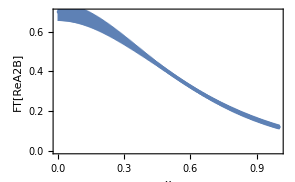
Gaussian-type fit for Re  for =-1
2 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot
a ⅇ^(-f η) (1+(d+c (1-k2/η^2-k1/η)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨1.696(39)⟩_(2902J)  ⟨0.097(12)⟩_(2902J)
⟨0.0752(15)⟩_(2902J) ⟨0.3173(28)⟩_(2902J)
⟨11.32(27)⟩_(2902J)  ⟨-25.6(20)⟩_(2902J)
⟨3.⟩_(2902J) | 20.7941 | 6002.69 | -Graphics-

```mathematica
FitetarangeListReA2B[2,-1,6,10]
```

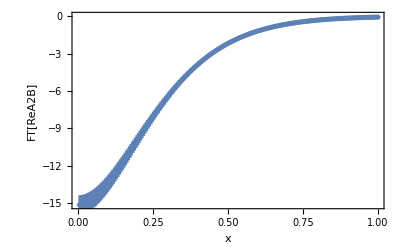
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
410 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot
a ⅇ^(-f η) (1+(d+c (1-k2/η^2-k1/η)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨-5.28(28)⟩_(2902J)   ⟨0.01938(26)⟩_(2902J)
⟨0.01938(26)⟩_(2902J) ⟨-0.097(25)⟩_(2902J)
⟨10.54(38)⟩_(2902J)   ⟨2.296(82)⟩_(2902J)
⟨3.⟩_(2902J) | 199.752 | 61537.5 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,4,10]
```

```mathematica
FitetarangeListReA2B[3,-1,5,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
510 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot
a ⅇ^(-f η) (1+(c+d) b_L^2+d b_T^2)^-j | a c
d f | ⟨1.553(59)⟩_(2902J)     ⟨0.01029(21)⟩_(2902J)
⟨0.01029(21)⟩_(2902J)   ⟨0.5255(63)⟩_(2902J)
⟨4.0000113(18)⟩_(2902J) | 39.5579 | 10492.9 | -Graphics-

```mathematica
FitetarangeListReA2B[2.5,-1,6,10]
```

Gaussian-type fit for Re  for =-1
2.5 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot
a ⅇ^(-f η) (1+(c+d) b_L^2+d b_T^2)^-j | a c
d f | ⟨2.082(86)⟩_(2902J)       ⟨0.01704(37)⟩_(2902J)
⟨0.01704(37)⟩_(2902J)     ⟨0.4769(57)⟩_(2902J)
⟨4.000000127(16)⟩_(2902J) | 40.7437 | 9788.5 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot
a ⅇ^(-f η) (1+(c+d) b_L^2+d b_T^2)^-j | a c
d f | ⟨1.97(12)⟩_(2902J)      ⟨0.01195(34)⟩_(2902J)
⟨0.01195(34)⟩_(2902J)   ⟨0.5385(88)⟩_(2902J)
⟨3.9999982(15)⟩_(2902J) | 25.2443 | 5563.74 | -Graphics-

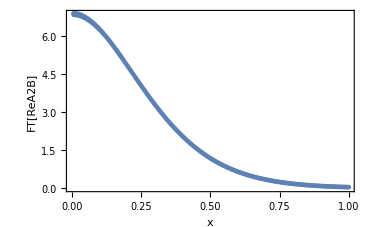
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot
a ⅇ^(-f η) (1+(d+c (1-k2/η^2-k1/η)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨2.628(11)⟩_(2902J)      ⟨0.01116(32)⟩_(2902J)
⟨0.01116(32)⟩_(2902J)    ⟨0.5854(40)⟩_(2902J)
⟨-1.125(28)⟩_(2902J)     ⟨-0.1664(44)⟩_(2902J)
⟨3.99999964(36)⟩_(2902J) | 31.0226 | 6776.93 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

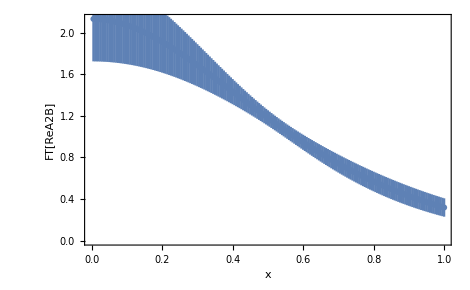
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot
a ⅇ^(-f η) (1+(d+c (1-k2/η^2-k1/η)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨2.64(22)⟩_(2902J)        ⟨0.067(21)⟩_(2902J)
⟨0.0401(16)⟩_(2902J)      ⟨0.492(11)⟩_(2902J)
⟨12.00(47)⟩_(2902J)       ⟨-34.9(28)⟩_(2902J)
⟨3.000000084(23)⟩_(2902J) | 1.91814 | 432.155 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

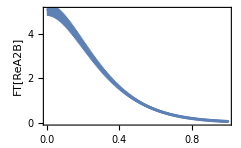
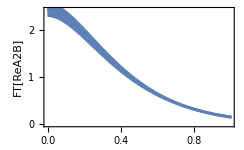
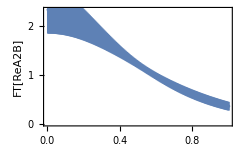
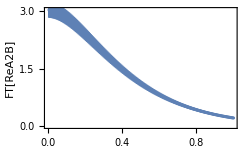
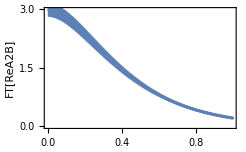
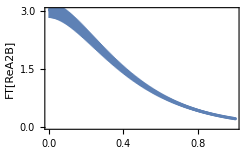
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot
a ⅇ^(-f η) (1+(c+d) b_L^2+d b_T^2)^-j | a c
d f | ⟨2.19(16)⟩_(2902J)   ⟨0.0218(44)⟩_(2902J)
⟨0.0218(44)⟩_(2902J) ⟨0.5382(88)⟩_(2902J)
⟨2.62(33)⟩_(2902J) | 24.778 | 5461.17 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1-k1/η)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 j | ⟨2.85(30)⟩_(2902J)  ⟨0.078(14)⟩_(2902J)
⟨0.078(14)⟩_(2902J) ⟨0.4625(89)⟩_(2902J)
⟨6.60(15)⟩_(2902J)  ⟨2.16(15)⟩_(2902J) | 2.113 | 474.746 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1-k2/η^2-k1/η)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2 | ⟨4.01(58)⟩_(2902J)  ⟨0.146(51)⟩_(2902J)
⟨0.094(18)⟩_(2902J) ⟨0.496(12)⟩_(2902J)
⟨12.27(50)⟩_(2902J) ⟨-36.2(28)⟩_(2902J)
⟨2.06(14)⟩_(2902J) | 1.56788 | 355.799 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1-k3/η^3-k2/η^2-k1/η)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
k3 j | ⟨4.01(58)⟩_(2902J)  ⟨0.093(18)⟩_(2902J)
⟨0.094(18)⟩_(2902J) ⟨0.496(12)⟩_(2902J)
⟨6.7(52)⟩_(2902J)   ⟨36(63)⟩_(2902J)
⟨-220(200)⟩_(2902J) ⟨2.06(14)⟩_(2902J) | 1.57467 | 357.703 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1-(k1 Log[η])/η)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 j | ⟨3.90(43)⟩_(2902J)  ⟨0.092(17)⟩_(2902J)
⟨0.092(17)⟩_(2902J) ⟨0.4929(86)⟩_(2902J)
⟨3.616(83)⟩_(2902J) ⟨2.07(14)⟩_(2902J) | 1.66147 | 375.863 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1-ⅇ^(-n η) k2-k1/η)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
n  j | ⟨3.98(58)⟩_(2902J)  ⟨0.093(18)⟩_(2902J)
⟨0.093(18)⟩_(2902J) ⟨0.495(12)⟩_(2902J)
⟨7.77(98)⟩_(2902J)  ⟨82(76)⟩_(2902J)
⟨0.64(45)⟩_(2902J)  ⟨2.06(14)⟩_(2902J) | 1.57582 | 357.952 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

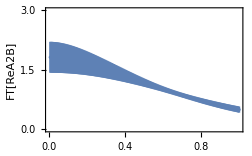
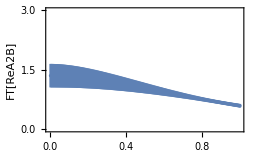
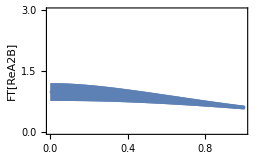
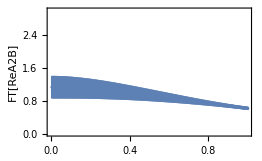
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
a ⅇ^(-f η) (1+(d+c (1-k1/η-(k2 Log[η])/η)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨4.01(58)⟩_(2902J)  ⟨0.240(89)⟩_(2902J)
⟨0.094(18)⟩_(2902J) ⟨0.496(12)⟩_(2902J)
⟨-4.50(52)⟩_(2902J) ⟨5.94(29)⟩_(2902J)
⟨2.06(14)⟩_(2902J) | 1.56865 | 355.966 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨4.01(58)⟩_(2902J)  ⟨0.43(17)⟩_(2902J)
⟨0.094(18)⟩_(2902J) ⟨0.496(12)⟩_(2902J)
⟨-5.81(33)⟩_(2902J) ⟨-4.86(14)⟩_(2902J)
⟨2.06(14)⟩_(2902J) | 1.56911 | 356.065 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1-k1/η+(k2 Log[η])/(√η))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨4.01(58)⟩_(2902J)  ⟨0.81(32)⟩_(2902J)
⟨0.094(18)⟩_(2902J) ⟨0.496(12)⟩_(2902J)
⟨0.409(88)⟩_(2902J) ⟨-1.284(19)⟩_(2902J)
⟨2.06(14)⟩_(2902J) | 1.56961 | 356.175 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1+(k1 √η)/(1+k2 η))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨4.01(58)⟩_(2902J)   ⟨0.59(27)⟩_(2902J)
⟨0.094(18)⟩_(2902J)  ⟨0.496(12)⟩_(2902J)
⟨-0.855(43)⟩_(2902J) ⟨0.179(17)⟩_(2902J)
⟨2.06(14)⟩_(2902J) | 1.57002 | 356.264 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

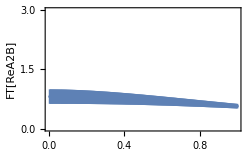
```mathematica
{{a ⅇ^(-f η) (1+(d+c (1+k2/η^0.8-k1/η^0.2)) Subscript[b, L]^2+d Subscript[b, T]^2)^-j, "a  c\nd  f\nk1 k2\nj", "⟨4.01(58)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)  ⟨1.18(48)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)\n⟨0.094(18)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\) ⟨0.496(12)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)\n⟨1.896(24)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\) ⟨1.342(73)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)\n⟨2.06(14)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)", "1.56956", "356.165", -Graphics-}}
```

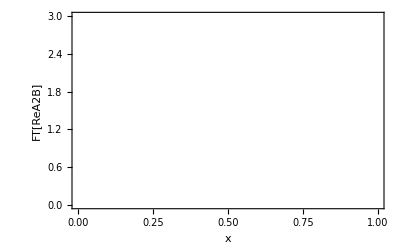
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
a ⅇ^(-f η) (1+(d+c (1-k1/η+k2 η^-g)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
g  j |                                                                3
⟨3.55(57)⟩_(2902J)         ⟨-7.11(24) × 10 ⟩_(2902J)
⟨0.089(18)⟩_(2902J)        ⟨0.484(11)⟩_(2902J)
                3                                              3
⟨-10.91(39) × 10 ⟩_(2902J) ⟨-8.51(32) × 10 ⟩_(2902J)
⟨535(17)⟩_(2902J)          ⟨2.09(14)⟩_(2902J) | 26.793 | 5830.07 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

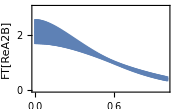
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
a ⅇ^(-f η) (1+(d+c (1+k2/η^1.5-k1/η)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨4.01(58)⟩_(2902J)  ⟨0.177(64)⟩_(2902J)
⟨0.094(18)⟩_(2902J) ⟨0.496(12)⟩_(2902J)
⟨18.14(78)⟩_(2902J) ⟨29.2(19)⟩_(2902J)
⟨2.06(14)⟩_(2902J) | 1.56824 | 355.877 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
a ⅇ^(-f η) (1+(d+c (1+k2/η^0.8-k1/η^0.2)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨4.01(58)⟩_(2902J)  ⟨1.18(48)⟩_(2902J)
⟨0.094(18)⟩_(2902J) ⟨0.496(12)⟩_(2902J)
⟨1.896(24)⟩_(2902J) ⟨1.342(73)⟩_(2902J)
⟨2.06(14)⟩_(2902J) | 1.56956 | 356.165 | -Graphics-

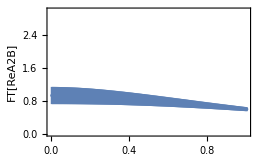
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
a ⅇ^(-f η) (1+(d+c (1+k2/η^0.7-k1/η^0.3)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨4.01(58)⟩_(2902J)  ⟨0.90(37)⟩_(2902J)
⟨0.094(18)⟩_(2902J) ⟨0.496(12)⟩_(2902J)
⟨2.965(56)⟩_(2902J) ⟨2.54(12)⟩_(2902J)
⟨2.06(14)⟩_(2902J) | 1.56955 | 356.162 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

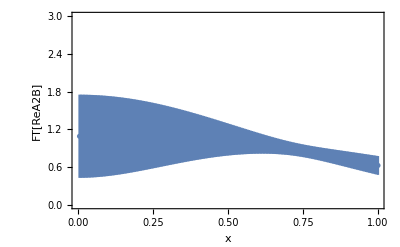
Gaussian-type fit for Re  for =-2
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
a ⅇ^(-f η) (1+(d+c (1+k2/η^0.8-k1/η^0.2)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨3.12(79)⟩_(2902J)  ⟨0.51(47)⟩_(2902J)
⟨0.045(19)⟩_(2902J) ⟨0.519(23)⟩_(2902J)
⟨1.899(65)⟩_(2902J) ⟨1.36(21)⟩_(2902J)
⟨3.15(67)⟩_(2902J) | 1.02324 | 237.065 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-2,6,10]
```

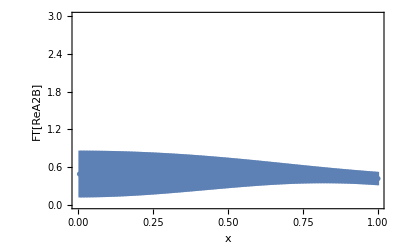
Gaussian-type fit for Re  for =-3
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
a ⅇ^(-f η) (1+(d+c (1+k2/η^0.8-k1/η^0.2)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨1.32(58)⟩_(2902J)      ⟨0.20(65)⟩_(2902J)
⟨0.006 ± 0.016⟩_(2902J) ⟨0.482(47)⟩_(2902J)
⟨1.914(45)⟩_(2902J)     ⟨1.42(13)⟩_(2902J)
⟨-17(19)⟩_(2902J) | 0.790895 | 186.415 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-3,6,10]
```

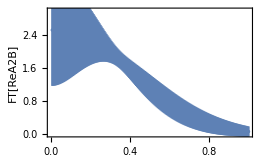
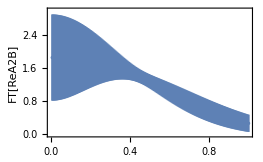
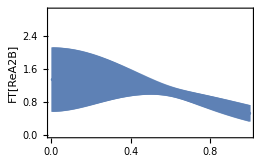
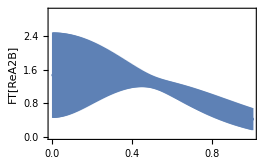
Gaussian-type fit for Re  for =-2
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
a ⅇ^(-f η) (1+(d+c (1-k1/η-(k2 Log[η])/η)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨3.12(80)⟩_(2902J)  ⟨0.108(86)⟩_(2902J)
⟨0.045(19)⟩_(2902J) ⟨0.519(23)⟩_(2902J)
⟨-4.4(14)⟩_(2902J)  ⟨5.84(71)⟩_(2902J)
⟨3.15(67)⟩_(2902J) | 1.02373 | 237.174 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨3.12(79)⟩_(2902J)  ⟨0.19(16)⟩_(2902J)
⟨0.045(19)⟩_(2902J) ⟨0.519(23)⟩_(2902J)
⟨-5.80(87)⟩_(2902J) ⟨-4.84(34)⟩_(2902J)
⟨3.15(67)⟩_(2902J) | 1.02347 | 237.117 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1-k1/η+(k2 Log[η])/(√η))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨3.12(79)⟩_(2902J)  ⟨0.36(31)⟩_(2902J)
⟨0.045(19)⟩_(2902J) ⟨0.519(23)⟩_(2902J)
⟨0.39(24)⟩_(2902J)  ⟨-1.283(49)⟩_(2902J)
⟨3.15(67)⟩_(2902J) | 1.02321 | 237.061 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1+(k1 √η)/(1+k2 η))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨3.12(79)⟩_(2902J)  ⟨0.24(26)⟩_(2902J)
⟨0.045(19)⟩_(2902J) ⟨0.519(23)⟩_(2902J)
⟨-0.80(14)⟩_(2902J) ⟨0.160(52)⟩_(2902J)
⟨3.15(67)⟩_(2902J) | 1.02301 | 237.016 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-2,6,10]
```

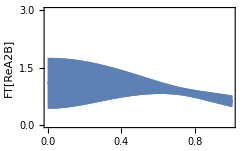
```mathematica
{{a ⅇ^(-f η) (1+(d+c (1+k2/η^0.8-k1/η^0.2)) Subscript[b, L]^2+d Subscript[b, T]^2)^-j, "a  c\nd  f\nk1 k2\nj", "⟨3.12(79)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)  ⟨0.51(47)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)\n⟨0.045(19)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\) ⟨0.519(23)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)\n⟨1.899(65)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\) ⟨1.36(21)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)\n⟨3.15(67)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)", "1.02324", "237.065", -Graphics-}}
```

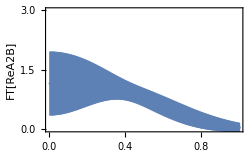
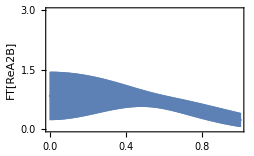
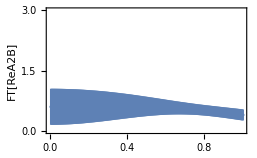
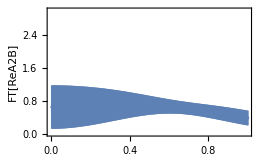
Gaussian-type fit for Re  for =-3
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
a ⅇ^(-f η) (1+(d+c (1-k1/η-(k2 Log[η])/η)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨1.33(58)⟩_(2902J)      ⟨0.04 ± 0.13⟩_(2902J)
⟨0.006 ± 0.016⟩_(2902J) ⟨0.482(47)⟩_(2902J)
⟨-4.90(95)⟩_(2902J)     ⟨6.07(55)⟩_(2902J)
⟨-17(19)⟩_(2902J) | 0.791211 | 186.484 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨1.32(58)⟩_(2902J)      ⟨0.07 ± 0.23⟩_(2902J)
⟨0.006 ± 0.016⟩_(2902J) ⟨0.482(47)⟩_(2902J)
⟨-6.09(60)⟩_(2902J)     ⟨-4.93(26)⟩_(2902J)
⟨-17(19)⟩_(2902J) | 0.791047 | 186.448 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1-k1/η+(k2 Log[η])/(√η))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨1.32(58)⟩_(2902J)      ⟨0.14(44)⟩_(2902J)
⟨0.006 ± 0.016⟩_(2902J) ⟨0.482(47)⟩_(2902J)
⟨0.31(15)⟩_(2902J)      ⟨-1.296(36)⟩_(2902J)
⟨-17(19)⟩_(2902J) | 0.790889 | 186.414 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1+(k1 √η)/(1+k2 η))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨1.32(58)⟩_(2902J)      ⟨0.1 ± 0.35⟩_(2902J)
⟨0.006 ± 0.016⟩_(2902J) ⟨0.482(47)⟩_(2902J)
⟨-0.799(59)⟩_(2902J)    ⟨0.160(25)⟩_(2902J)
⟨-17(19)⟩_(2902J) | 0.790686 | 186.369 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-3,6,10]
```

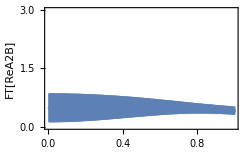
```mathematica
{{a ⅇ^(-f η) (1+(d+c (1+k2/η^0.8-k1/η^0.2)) Subscript[b, L]^2+d Subscript[b, T]^2)^-j, "a  c\nd  f\nk1 k2\nj", "⟨1.32(58)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)      ⟨0.20(65)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)\n⟨0.006 ± 0.016\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\) ⟨0.482(47)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)\n⟨1.914(45)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)     ⟨1.42(13)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)\n⟨-17(19)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)", "0.790895", "186.415", -Graphics-}}
```

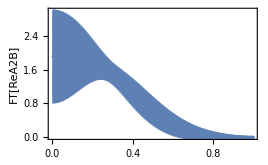
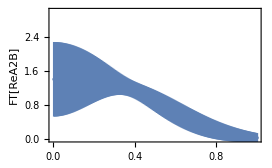
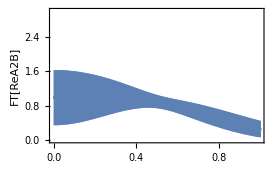
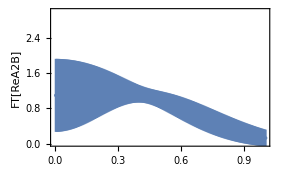
Gaussian-type fit for Re  for =-3
3 are SELECTED for fit!
510 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
a ⅇ^(-f η) (1+(d+c (1-k1/η-(k2 Log[η])/η)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨1.50(43)⟩_(2902J)      ⟨0.041(51)⟩_(2902J)
⟨0.009 ± 0.011⟩_(2902J) ⟨0.503(37)⟩_(2902J)
⟨-3.15(99)⟩_(2902J)     ⟨5.06(62)⟩_(2902J)
⟨1.7(84)⟩_(2902J) | 0.989738 | 274.301 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨1.50(43)⟩_(2902J)      ⟨0.072(91)⟩_(2902J)
⟨0.009 ± 0.011⟩_(2902J) ⟨0.503(37)⟩_(2902J)
⟨-5.07(72)⟩_(2902J)     ⟨-4.50(33)⟩_(2902J)
⟨1.8(84)⟩_(2902J) | 0.989156 | 274.148 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1-k1/η+(k2 Log[η])/(√η))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨1.50(43)⟩_(2902J)      ⟨0.14(18)⟩_(2902J)
⟨0.009 ± 0.011⟩_(2902J) ⟨0.503(37)⟩_(2902J)
⟨0.53(17)⟩_(2902J)      ⟨-1.243(47)⟩_(2902J)
⟨1.8(84)⟩_(2902J) | 0.988545 | 273.987 | -Graphics-
a ⅇ^(-f η) (1+(d+c (1+(k1 √η)/(1+k2 η))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨1.50(43)⟩_(2902J)      ⟨0.09 ± 0.13⟩_(2902J)
⟨0.009 ± 0.011⟩_(2902J) ⟨0.503(37)⟩_(2902J)
⟨-0.86(12)⟩_(2902J)     ⟨0.184(50)⟩_(2902J)
⟨1.8(83)⟩_(2902J) | 0.988079 | 273.865 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-3,5,10]
```

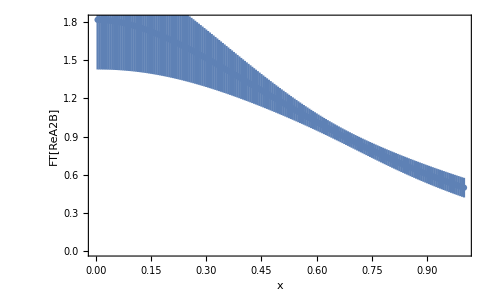
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot
a ⅇ^(-f η) (1+(d+c (1-k1/η-(k2 Log[η])/η)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨4.01(58)⟩_(2902J)  ⟨0.240(89)⟩_(2902J)
⟨0.094(18)⟩_(2902J) ⟨0.496(12)⟩_(2902J)
⟨-4.50(52)⟩_(2902J) ⟨5.94(29)⟩_(2902J)
⟨2.06(14)⟩_(2902J) | 1.56865 | 355.966 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

```mathematica
FitetarangeListReA2B[3,-4,5,9]
```

$Aborted

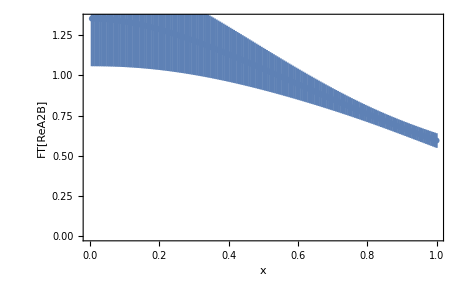
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot
a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨4.01(58)⟩_(2902J)  ⟨0.43(17)⟩_(2902J)
⟨0.094(18)⟩_(2902J) ⟨0.496(12)⟩_(2902J)
⟨-5.81(33)⟩_(2902J) ⟨-4.86(14)⟩_(2902J)
⟨2.06(14)⟩_(2902J) | 1.56911 | 356.065 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

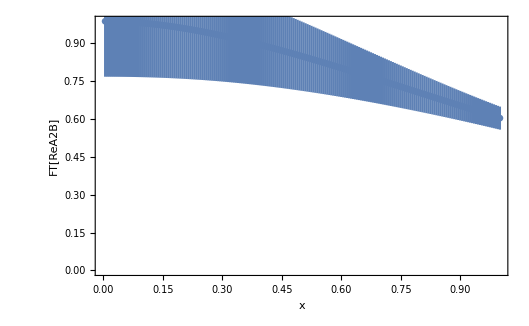
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot
a ⅇ^(-f η) (1+(d+c (1-k1/η+(k2 Log[η])/(√η))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨4.01(58)⟩_(2902J)  ⟨0.81(32)⟩_(2902J)
⟨0.094(18)⟩_(2902J) ⟨0.496(12)⟩_(2902J)
⟨0.409(88)⟩_(2902J) ⟨-1.284(19)⟩_(2902J)
⟨2.06(14)⟩_(2902J) | 1.56961 | 356.175 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

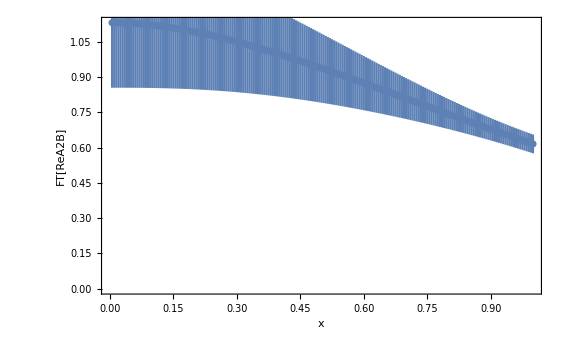
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot
a ⅇ^(-f η) (1+(d+c (1+(k1 √η)/(1+k2 η))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨4.01(58)⟩_(2902J)   ⟨0.59(27)⟩_(2902J)
⟨0.094(18)⟩_(2902J)  ⟨0.496(12)⟩_(2902J)
⟨-0.855(43)⟩_(2902J) ⟨0.179(17)⟩_(2902J)
⟨2.06(14)⟩_(2902J) | 1.57002 | 356.264 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

$Aborted

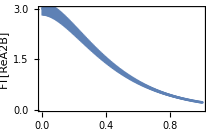
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot
a ⅇ^(-f η) (1+(d+c (1-k1/η+k2 η^-q)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
q  j | ⟨3.99(58)⟩_(2902J)  ⟨0.093(18)⟩_(2902J)
⟨0.093(18)⟩_(2902J) ⟨0.495(12)⟩_(2902J)
                                                        3
⟨7.5(15)⟩_(2902J)   ⟨-15.3(58) × 10 ⟩_(2902J)
⟨3.5(32)⟩_(2902J)   ⟨2.06(14)⟩_(2902J) | 1.57504 | 357.784 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

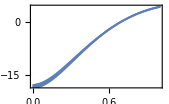
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot
a ⅇ^(-f η) (1+(d+c (1-k1 η^(-Abs[p])+k2 η^(-Abs[q]))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
p  q
j | ⟨4.00(58)⟩_(2902J)   ⟨9.81(31)⟩_(2902J)
⟨0.094(18)⟩_(2902J)  ⟨0.495(12)⟩_(2902J)
⟨0.02 ± 6.6⟩_(2902J) ⟨-504.6(87)⟩_(2902J)
⟨-1.47(77)⟩_(2902J)  ⟨-66.0(35)⟩_(2902J)
⟨2.06(14)⟩_(2902J) | 1.95389 | 440.039 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

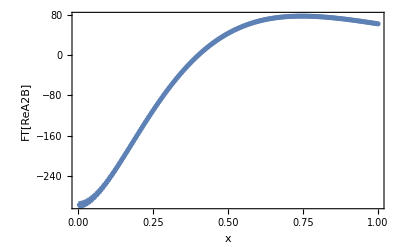
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot
a ⅇ^(-f η) (1+(d+c (1-k1 η^-p+k2 η^-q)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
p  q
j | ⟨3.91(58)⟩_(2902J)        ⟨23.67(69)⟩_(2902J)
⟨0.098(18)⟩_(2902J)       ⟨0.488(12)⟩_(2902J)
               3                                               3
⟨-3.79(11) × 10 ⟩_(2902J) ⟨-105.9(21) × 10 ⟩_(2902J)
⟨-174.1(52)⟩_(2902J)      ⟨-420.1(88)⟩_(2902J)
⟨2.03(14)⟩_(2902J) | 43.0037 | 9306.8 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

```mathematica
Hypergeometric1F1[0.5+1,0.5+3+2,I*2]
Hypergeometric1F1[0.5+1,0.5+3+2,2]
```

0.806687+0.484038 ⅈ

1.8428

```mathematica
FitetarangeListReA2BHyperGeo[bminForFit_,momL_,etamin_,etamax_]:=Module[{fitJKA2B,dataforfitA2B,results={}},
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];

modelfitA2B[x1_,x2_,x3_,{a_,d_,f_,alpha_,beta_}]:=a*Exp[-f*x1]*Exp[-d*(x2^2+x3^2)]*Beta[alpha+1,beta+1]*Re[Hypergeometric1F1[alpha+1,alpha+beta+2,I*x2]];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,d,f,alphap,betap}],{{a,2.4},{d,0.07},{f,0.4},{alphap,0.01},{betap,0.01}},{n,bL,bT},modelfitA2B];
AppendTo[results,{modelfitA2B[,,,{a, d,f,alpha, beta}],"{a,d,f,alpha,beta}",OutputForm[FitParameters/.fitJKA2B],OutputForm[chisquareDoF/.fitJKA2B]}];

Print["Gaussian-type fit for Re  for =",momL,"\n","",bminForFit," are SELECTED for fit!\n",etamin,"",etamax," are SELECTED for fit!\n \n",TableForm[results,TableHeadings->{None,{"Model Expression","Params List","Fitted Values","/DoF"}},TableSpacing->{1,2}]];]
```

```mathematica
FitetarangeListReA2BHyperGeo[3,-1,6,10]
```

$Aborted

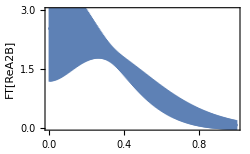
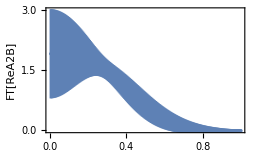
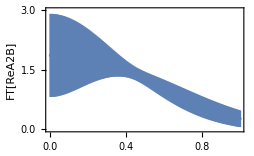
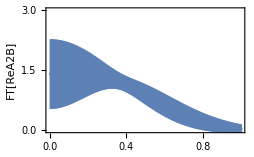
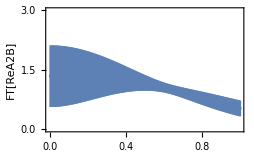
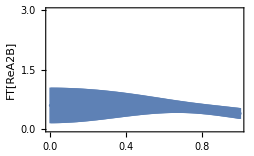
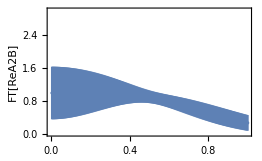
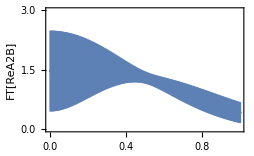
```mathematica
{{"Model Expression"                                                                                     "PL = -1"                                                   "PL = -2"                                                          "PL = -3"}, {a ⅇ^(-f η) (1+(d+c (1-k1/η-(k2 Log[η])/η)) Subscript[b, L]^2+d Subscript[b, T]^2)^-j    -Graphics--Graphics--Graphics--Graphics-}, {a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) Subscript[b, L]^2+d Subscript[b, T]^2)^-j            -Graphics--Graphics--Graphics--Graphics-}, {a ⅇ^(-f η) (1+(d+c (1-k1/η+(k2 Log[η])/(√η))) Subscript[b, L]^2+d Subscript[b, T]^2)^-j   -Graphics--Graphics--Graphics--Graphics-}, {a ⅇ^(-f η) (1+(d+c (1+(k1 √η)/(1+k2 η))) Subscript[b, L]^2+d Subscript[b, T]^2)^-j                -Graphics--Graphics--Graphics--Graphics-}}
```

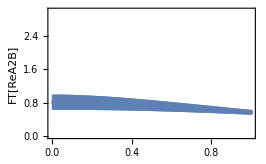
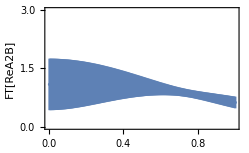
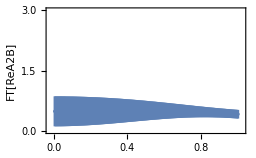
```mathematica
{{"Model Expression"                                                                                     "PL = -1"                                                   "PL = -2"                                                          "PL = -3"}, {a ⅇ^(-f η) (1+(d+c (1-k1/η-(k2 Log[η])/η)) Subscript[b, L]^2+d Subscript[b, T]^2)^-j    -Graphics--Graphics--Graphics-}, {a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) Subscript[b, L]^2+d Subscript[b, T]^2)^-j            -Graphics--Graphics--Graphics-}, {a ⅇ^(-f η) (1+(d+c (1-k1/η+(k2 Log[η])/(√η))) Subscript[b, L]^2+d Subscript[b, T]^2)^-j   -Graphics--Graphics--Graphics-}, {a ⅇ^(-f η) (1+(d+c (1+(k1 √η)/(1+k2 η))) Subscript[b, L]^2+d Subscript[b, T]^2)^-j                -Graphics--Graphics--Graphics-
a ⅇ^(-f η) (1+(d+c (1+k2/η^0.8-k1/η^0.2)) Subscript[b, L]^2+d Subscript[b, T]^2)^-j  -Graphics-  -Graphics--Graphics-}}
```

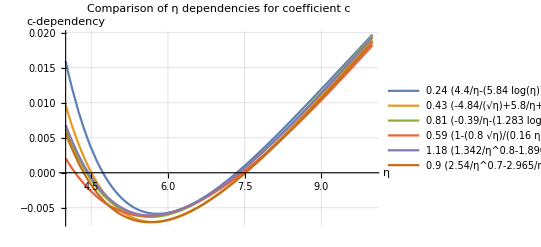

```mathematica
c1[η_,k1_,k2_]:=(1-k1/η-(k2*Log[η])/η)*0.240
c2[η_,k1_,k2_]:=(1-k1/η+k2/Sqrt[η])*0.43
c3[η_,k1_,k2_]:=(1-k1/η+(k2*Log[η])/Sqrt[η])0.81
c4[η_,k1_,k2_]:=(1+(k1*Sqrt[η])/(1+k2*η))0.59
c5[η_,k1_,k2_]:=(1-k1/η^0.2+k2/η^0.8)*1.18
c6[η_,k1_,k2_]:=(1-k1/η^0.3+k2/η^0.7)*0.9 


Plot[{c1[η,-4.50,5.94],c2[η,-5.81,-4.86],c3[η,0.409,-1.284],c4[η,-0.855,0.179],c5[η,1.896,1.342],c6[η,2.965,2.54]},{η,4,10},PlotRange->All,PlotLegends->{c1["η",-4.4,5.84],c2["η",-5.80,-4.84],c3["η",0.39,-1.283],c4["η",-0.80,0.160],c5["η",1.896,1.342],c6["η",2.965,2.54]},AxesLabel->{"η","c-dependency"},PlotLabel->"Comparison of η dependencies for coefficient c",GridLines->Automatic]
```

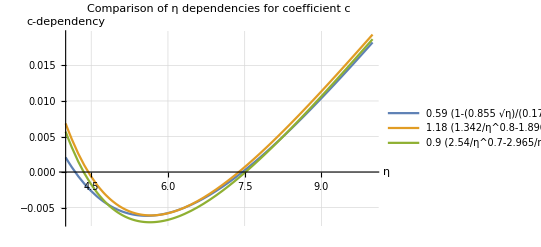

```mathematica
Plot[{c4[η,-0.855,0.179],c5[η,1.896,1.342],c6[η,2.965,2.54]},{η,4,10},PlotRange->All,PlotLegends->{c4[η,-0.855,0.179],c5["η",1.896,1.342],c6["η",2.965,2.54]},AxesLabel->{"η","c-dependency"},PlotLabel->"Comparison of η dependencies for coefficient c",GridLines->Automatic]
```

```mathematica
(*PlotAbLfordiffbLbT[ampname_,P1_, etavalue_, bnum_, Nnum_]:=(
Print[Nnum ampname," =>  = ",P1," ,eta = ", etavalue];
(*bTlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],bT]];
bLlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],bL]];*)
rawData=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bNum->bnum}],{bL,bT}];
Print[rawData//Sort];
filteredData=Select[rawData,(#[[1]]^2+#[[2]]^2)>=0^2&];
Print[filteredData//Sort];
bLlist=Union[filteredData[[All,1]]];
bTlist=Union[filteredData[[All,2]]];
Print[bLlist];
Print[bTlist];
PlotbLforDiffbTList={};
Do[
bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bT->bTi, bNum->bnum}],{bL,data}];
bLAmp=Select[bLAmp,MemberQ[bLlist,#[[1]]]&];
AppendTo[PlotbLforDiffbTList,bLAmp];
 ,{bTi,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bTi]]],{bTi, Length[bTlist]}],FrameLabel->{, Nnum ampname }, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bTlist[[bTi]]],{bTi,Length[bTlist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bL_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotbL,"PDF",ImageResolution->600];
PlotbTforDiffbLList={};
Do[
bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bL->bLi, bNum->bnum}],{bT,data}];
bLAmp=Select[bLAmp,MemberQ[bTlist,#[[1]]]&];
AppendTo[PlotbTforDiffbLList,bLAmp];
 ,{bLi,bLlist}];
PlotbT= ErrorListPlot[Table[MakeErrBars[PlotbTforDiffbLList[[bLi]]],{bLi, Length[bLlist]}],FrameLabel->{,ampname b bnum}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bLlist[[bLi]]],{bLi,Length[bLlist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bT_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotbT,"PDF",ImageResolution->600];GraphicsRow[{PlotbL,PlotbT},ImageSize->Full]
)*)
PlotAbLfordiffbLbT[ampname_,P1_,etavalue_,bnum_,Nnum_]:=(Print[Nnum ampname," => PL = ",P1," ,eta = ",etavalue];
rawData=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bNum->bnum}],{bL,bT}];
(*Filter pairs satisfying the radius condition*)filteredPairs=Select[rawData,Sqrt[#[[1]]^2+#[[2]]^2]>=3&];

bLlist=Union[filteredPairs[[All,1]]];
bTlist=Union[filteredPairs[[All,2]]];

(*Convert to a lookup set for fast pair membership testing*)validPairSet=Association[Rule[#,True]&/@filteredPairs];
(*---Plot vs bL (curves for different bT)---*)PlotbLforDiffbTList={};
Do[bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bT->bTi,bNum->bnum}],{bL,data}];
(*Keep only pairs {bL,bTi} that passed the radius filter*)bLAmp=Select[bLAmp,KeyExistsQ[validPairSet,{#[[1]],bTi}]&];
AppendTo[PlotbLforDiffbTList,bLAmp];,{bTi,bTlist}];
PlotbL=ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bTi]]],{bTi,Length[bTlist]}],FrameLabel->{Subscript[b,L],Nnum ampname},Frame->True,PlotRange->Full,PlotLegends->Table["bT = "<>ToString[bTlist[[bTi]]],{bTi,Length[bTlist]}],ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bL_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotbL,"PDF",ImageResolution->600];
(*---Plot vs bT (curves for different bL)---*)PlotbTforDiffbLList={};
Do[bTAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bL->bLi,bNum->bnum}],{bT,data}];
(*Keep only pairs {bLi,bT} that passed the radius filter*)bTAmp=Select[bTAmp,KeyExistsQ[validPairSet,{bLi,#[[1]]}]&];
AppendTo[PlotbTforDiffbLList,bTAmp];,{bLi,bLlist}];
PlotbT=ErrorListPlot[Table[MakeErrBars[PlotbTforDiffbLList[[bLi]]],{bLi,Length[bLlist]}],FrameLabel->{Subscript[b,T],ampname b bnum},Frame->True,PlotRange->Full,PlotLegends->Table["bL = "<>ToString[bLlist[[bLi]]],{bLi,Length[bLlist]}],ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bT_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotbT,"PDF",ImageResolution->600];
GraphicsRow[{PlotbL,PlotbT},ImageSize->Full])
PlotAfordiffBPbbsq[ampname_,P1_, etavalue_, bnum_, Nnum_]:=(
Print[Nnum ampname," =>  = ",P1," ,eta = ", etavalue];
(*bsquarelist= Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],bsquare]];
bsquarelist = Select[bsquarelist,9<=#&];
Pb32by2Pilist= Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],Pb32by2Pi]];
Pb32by2Pilist = Select[Pb32by2Pilist,#<=-3&&#>=3&];*)

rawData=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,bNum->bnum}],{bsquare,Pb32by2Pi}];
filteredData=Select[rawData,#[[1]]>=0&];
Print[filteredData//Sort];
bsquarelist=Union[filteredData[[All,1]]];
Pb32by2Pilist=Union[filteredData[[All,2]]];
PlotPbforDiffbsq={};
Do[
PbAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,bsquare->bsqi, bNum->bnum}],{Pb32by2Pi,data}];
AppendTo[PlotPbforDiffbsq,PbAmp];
 ,{bsqi,bsquarelist}];
PlotbP= ErrorListPlot[Table[MakeErrBars[PlotPbforDiffbsq[[bsqi]]],{bsqi, Length[bsquarelist]}],FrameLabel->{ , Nnum ampname }, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bsquarelist[[bsqi]]],{bsqi,Length[bsquarelist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bP_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotbP,"PDF",ImageResolution->600];
PlotbsqforDiffPb={};
Do[
bsqAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,Pb32by2Pi->Pbi, bNum->bnum}],{bsquare,data}];
bsqAmp=Select[bsqAmp,#[[1]]>=9&];
AppendTo[PlotbsqforDiffPb,bsqAmp];
 ,{Pbi,Pb32by2Pilist}];
Plotbsq= ErrorListPlot[Table[MakeErrBars[PlotbsqforDiffPb[[Pbi]]],{Pbi, Length[Pb32by2Pilist]}],FrameLabel->{,Nnum ampname }, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[Pb32by2Pilist[[Pbi]]],{Pbi,Length[Pb32by2Pilist]}], ImageSize->450];
(*Export["/Users/hariprashadravikumar/Downloads/bsq_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotbsq,"PDF",ImageResolution->600];*)
GraphicsRow[{PlotbP,Plotbsq},ImageSize->Full]
)
```

```mathematica
PlotAbLfordiffbLbT[A2B,-1,9, even, "Re"]
PlotAbLfordiffbLbT[A2B,-1,9, odd, "Im"]
PlotAbLfordiffbLbT[A12B,-1,9, even, "Re"]
```

Re A2B => PL = -1 ,eta = 9

-Graphics-

Im A2B => PL = -1 ,eta = 9

-Graphics-

Re A12B => PL = -1 ,eta = 9

-Graphics-

```mathematica
PlotAbLfordiffbLbT[A2B,-1,9, even, "Re"]
```

Re A2B => PL = -1 ,eta = 9

-Graphics-

```mathematica
PlotAbLfordiffbLbT[A2B,-1,9, odd, "Im"]
```

Im A2B => PL = -1 ,eta = 9

-Graphics-

```mathematica
PlotAbLfordiffbLbT[A12B,-3,9, even, "Re"]
```

Re A12B => PL = -3 ,eta = 9

{{-8,-2},{-8,2},{-6,-3},{-6,3},{-5,-5},{-5,5},{-4,-4},{-4,-2},{-4,-1},{-4,1},{-4,2},{-4,4},{-3,-6},{-3,-3},{-3,3},{-3,6},{-2,-4},{-2,-2},{-2,2},{-2,4},{0,-7},{0,-6},{0,-5},{0,-4},{0,-3},{0,3},{0,4},{0,5},{0,6},{0,7},{2,-4},{2,-2},{2,2},{2,4},{3,-6},{3,-3},{3,3},{3,6},{4,-4},{4,-2},{4,-1},{4,1},{4,2},{4,4},{5,-5},{5,5},{6,-3},{6,3},{8,-2},{8,2}}

{-8,-6,-5,-4,-3,-2,0,2,3,4,5,6,8}

{-7,-6,-5,-4,-3,-2,-1,1,2,3,4,5,6,7}

-Graphics-

```mathematica
PlotAbLfordiffbLbT[A12B,-3,9, even, "Re"]
```

Re A12B => PL = -3 ,eta = 9

{{-8,-2},{-8,2},{-6,-3},{-6,3},{-5,-5},{-5,5},{-4,-4},{-4,-2},{-4,-1},{-4,1},{-4,2},{-4,4},{-3,-6},{-3,-3},{-3,3},{-3,6},{-2,-4},{-2,-2},{-2,2},{-2,4},{0,-7},{0,-6},{0,-5},{0,-4},{0,-3},{0,3},{0,4},{0,5},{0,6},{0,7},{2,-4},{2,-2},{2,2},{2,4},{3,-6},{3,-3},{3,3},{3,6},{4,-4},{4,-2},{4,-1},{4,1},{4,2},{4,4},{5,-5},{5,5},{6,-3},{6,3},{8,-2},{8,2}}

{-8,-6,-5,-4,-3,-2,0,2,3,4,5,6,8}

{-7,-6,-5,-4,-3,-2,-1,1,2,3,4,5,6,7}

-Graphics-

```mathematica
PlotAbLfordiffbLbT[A12B,-3,9, even, "Re"]
```

Re A12B => PL = -3 ,eta = 9

{{-8,-2},{-8,2},{-6,-3},{-6,3},{-5,-5},{-5,5},{-4,-4},{-4,-2},{-4,-1},{-4,1},{-4,2},{-4,4},{-3,-6},{-3,-3},{-3,3},{-3,6},{-2,-4},{-2,4},{0,-7},{0,-6},{0,-5},{0,-4},{0,-3},{0,3},{0,4},{0,5},{0,6},{0,7},{2,-4},{2,4},{3,-6},{3,-3},{3,3},{3,6},{4,-4},{4,-2},{4,-1},{4,1},{4,2},{4,4},{5,-5},{5,5},{6,-3},{6,3},{8,-2},{8,2}}

{-8,-6,-5,-4,-3,-2,0,2,3,4,5,6,8}

{-7,-6,-5,-4,-3,-2,-1,1,2,3,4,5,6,7}

-Graphics-

```mathematica
PlotAbLfordiffbLbT[A2B,-4,8, even, "Re"]
```

Re A2B =>  = -4 ,eta = 8

{{-8,2},{-6,-3},{-6,3},{-5,-5},{-5,5},{-4,-4},{-4,-2},{-4,-1},{-4,1},{-4,2},{-4,4},{-3,-6},{-3,-3},{-3,3},{-3,6},{-2,-4},{-2,4},{0,-7},{0,-6},{0,-5},{0,-4},{0,-3},{0,3},{0,4},{0,5},{0,6},{0,7},{2,-4},{2,4},{3,-6},{3,-3},{3,3},{3,6},{4,-4},{4,-2},{4,-1},{4,1},{4,2},{4,4},{5,-5},{5,5},{6,-3},{6,3},{8,-2},{8,2}}

-Graphics-

```mathematica
PlotAfordiffBPbbsq[A2B,-1,8, even, "Re"]
```

Re A2B =>  = -1 ,eta = 8

{{0,0},{1,0},{2,-1},{2,1},{4,0},{5,-2},{5,-1},{5,1},{5,2},{8,-2},{8,2},{9,0},{16,0},{17,-4},{17,4},{18,-3},{18,3},{20,-4},{20,-2},{20,2},{20,4},{25,0},{32,-4},{32,4},{36,0},{45,-6},{45,-3},{45,3},{45,6},{49,0},{50,-5},{50,5},{68,-8},{68,8}}

-Graphics-

```mathematica
PlotRatiosBPbbsq[ampname_,P1_,etavalue_,bnum_,Nnum_]:=Module[{bsquarelist,Pb32by2Pilist,PlotPbforDiffbsq,refData,RatioDataList,PlotRatio},(*1. Get b^2 and P.b lists*)bsquarelist=Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,bNum->bnum}],bsquare]];
bsquarelist=Select[bsquarelist,9<=#&];
(*2. Get the reference data (first b^2 in the list)*)refBSQ=First[bsquarelist];
refData=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,bsquare->refBSQ,bNum->bnum}],{Pb32by2Pi,data}];
RatioDataList={};
(*3. Loop through b^2 and compute Ratio:F(Pb,bsq_i)/F(Pb,bsq_ref)*)Do[currentData=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,bsquare->bsqi,bNum->bnum}],{Pb32by2Pi,data}];
(*Dividing the'data' column while keeping the'Pb' column the same*)(*This assumes Pb points match exactly across different b^2 slices*)ratioPoints=Table[{currentData[[i,1]],currentData[[i,2]]/refData[[i,2]]},{i,Length[currentData]}];
AppendTo[RatioDataList,ratioPoints];,{bsqi,bsquarelist}];
(*4. Plot the Ratios*)PlotRatio=ListLinePlot[RatioDataList,Frame->True,PlotRange->All,FrameLabel->{"P.b (32/2π)","Ratio to (b^2 = "<>ToString[refBSQ]<>")"},PlotLegends->Table["(b)^2 = "<>ToString[bsq],{bsq,bsquarelist}],PlotStyle->Thick,ImageSize->500,PlotLabel->Style["Factorization Test (Ratio)",Bold,14]];
Print["Ratio Plot Generated for Reference (b)^2 = ",refBSQ];
Return[PlotRatio]]
PlotRatiosBPbbsq[A2B,-1,10, even, "Re"]
```

Ratio Plot Generated for Reference (b)^2 = 9

-Graphics-

```mathematica
(*── 1. Fetch data ───────────────────────────────────────────────*)rawData=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->-1,etav->8,bNum->even}],{bL,bT,data}   (*adjust "val" to whatever your amplitude column is called*)];
(*rawData is assumed to be a list of {bL,bT,value} triples*)
(*If your DB returns only {bL,bT},see note at the bottom*)

(*── 2. Fold bT-> |bT|and collect unique axis values ───────────*)
foldedData={#[[1]],Abs[#[[2]]],#[[3]]}&/@rawData

bLVals=Sort@DeleteDuplicates[foldedData[[All,1]]];
bTVals=Sort@DeleteDuplicates[foldedData[[All,2]]];(* |bT|*)nL=Length[bLVals];
nT=Length[bTVals];

bLIndex=AssociationThread[bLVals->Range[nL]];
bTIndex=AssociationThread[bTVals->Range[nT]];

(*── 3. Build the matrix (missing entries=0) ────────────────────*)
M=ConstantArray[0.,{nL,nT}]
```

{{0,0,⟨0.6282(34)⟩_(RowBox[{)},{0,1,⟨0.2615(18)⟩_(RowBox[{)},{0,2,⟨0.06603(85)⟩_(RowBox[{)},{0,3,⟨0.02313(67)⟩_(RowBox[{)},{0,4,⟨0.01148(63)⟩_(RowBox[{)},{0,5,⟨0.00583(56)⟩_(RowBox[{)},{0,6,⟨0.00315(50)⟩_(RowBox[{)},{0,7,⟨0.00206(48)⟩_(RowBox[{)},{0,1,⟨0.2609(17)⟩_(RowBox[{)},{0,2,⟨0.06549(86)⟩_(RowBox[{)},{0,3,⟨0.02259(68)⟩_(RowBox[{)},{0,4,⟨0.01061(61)⟩_(RowBox[{)},{0,5,⟨0.00549(57)⟩_(RowBox[{)},{0,6,⟨0.00283(52)⟩_(RowBox[{)},{0,7,⟨0.00152(47)⟩_(RowBox[{)},{1,1,⟨0.1549(11)⟩_(RowBox[{)},{2,2,⟨0.02847(52)⟩_(RowBox[{)},{3,3,⟨0.00936(41)⟩_(RowBox[{)},{4,4,⟨0.00342(35)⟩_(RowBox[{)},{5,5,⟨0.00143(31)⟩_(RowBox[{)},{1,2,⟨0.05079(67)⟩_(RowBox[{)},{2,4,⟨0.00808(41)⟩_(RowBox[{)},{3,6,⟨0.00179(34)⟩_(RowBox[{)},{2,1,⟨0.05738(61)⟩_(RowBox[{)},{4,2,⟨0.00848(44)⟩_(RowBox[{)},{6,3,⟨0.00170(35)⟩_(RowBox[{)},{4,1,⟨0.01078(45)⟩_(RowBox[{)},{8,2,⟨850(320) × 10⟩_(RowBox[{)},{1,1,⟨0.1545(11)⟩_(RowBox[{)},{2,2,⟨0.02798(50)⟩_(RowBox[{)},{3,3,⟨0.00878(42)⟩_(RowBox[{)},{4,4,⟨0.00355(37)⟩_(RowBox[{)},{5,5,⟨0.00206(31)⟩_(RowBox[{)},{1,2,⟨0.05055(68)⟩_(RowBox[{)},{2,4,⟨0.00770(42)⟩_(RowBox[{)},{3,6,⟨0.00224(36)⟩_(RowBox[{)},{2,1,⟨0.05724(58)⟩_(RowBox[{)},{4,2,⟨0.00775(45)⟩_(RowBox[{)},{6,3,⟨0.00186(33)⟩_(RowBox[{)},{4,1,⟨0.01065(44)⟩_(RowBox[{)},{8,2,⟨790(330) × 10⟩_(RowBox[{)},{-1,1,⟨0.1549(11)⟩_(RowBox[{)},{-2,2,⟨0.02847(52)⟩_(RowBox[{)},{-3,3,⟨0.00936(41)⟩_(RowBox[{)},{-4,4,⟨0.00342(35)⟩_(RowBox[{)},{-5,5,⟨0.00143(31)⟩_(RowBox[{)},{-1,2,⟨0.05079(67)⟩_(RowBox[{)},{-2,4,⟨0.00808(41)⟩_(RowBox[{)},{-3,6,⟨0.00179(34)⟩_(RowBox[{)},{-2,1,⟨0.05738(61)⟩_(RowBox[{)},{-4,2,⟨0.00848(44)⟩_(RowBox[{)},{-6,3,⟨0.00170(35)⟩_(RowBox[{)},{-4,1,⟨0.01078(45)⟩_(RowBox[{)},{-8,2,⟨850(320) × 10⟩_(RowBox[{)},{-1,1,⟨0.1545(11)⟩_(RowBox[{)},{-2,2,⟨0.02798(50)⟩_(RowBox[{)},{-3,3,⟨0.00878(42)⟩_(RowBox[{)},{-4,4,⟨0.00355(37)⟩_(RowBox[{)},{-5,5,⟨0.00206(31)⟩_(RowBox[{)},{-1,2,⟨0.05055(68)⟩_(RowBox[{)},{-2,4,⟨0.00770(42)⟩_(RowBox[{)},{-3,6,⟨0.00224(36)⟩_(RowBox[{)},{-2,1,⟨0.05724(58)⟩_(RowBox[{)},{-4,2,⟨0.00775(45)⟩_(RowBox[{)},{-6,3,⟨0.00186(33)⟩_(RowBox[{)},{-4,1,⟨0.01065(44)⟩_(RowBox[{)}}

{{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.}}